# QNM Amplitude: Time and Frequency domain analysis

```mathematica
Quit[]
```

```mathematica
Clear["Global`*"]
<<MaTeX`
SetDirectory[NotebookDirectory[]];
$Assumptions={M>0}
DirName=NotebookDirectory[];
```

{M>0}

## Parameters

## Physical Parameters

### Wave equation Parameters

```mathematica
Mbh=rh/2;
λ=rh;
spin=2;
l=2;
```

### Bump Parameters

```mathematica
ModelName="BumpPT";
 ao= 10;(*115722/10000;*) (*120000/10000;*)
 ϵ=0;(*204/100000;*)
```

## Numerical Parameters

```mathematica
Prec=10*MachinePrecision;


Nz$dom0=75;
Nz$dom1=75;


Nz$QNMload$dom0=75;
Nz$QNMload$dom1=75;
```

### QNM Selection

```mathematica
N$QNM$max=3;
```

## Schwarzschild Spacetime

## Metric Function

```mathematica
a=1-rh/r;
b=a;
f=FullSimplify[Sqrt[a*b], Assumptions->{rh>0, r>rh}];
ζ$of$r=FullSimplify[Sqrt[a/b], Assumptions->{rh>0, r>rh}];
```

```mathematica
m=r/2*(1-b);

fAsymp=Normal@Series[f,{r,Infinity,1}]//Expand;
M$ADM=-Coefficient[fAsymp,r,-1]/2//FullSimplify;
SubsM={M->M$ADM}
```

{M→rh/2}

## Hyperboloidal Formulation

## Radial Compactfication

### Areal Radius

```mathematica
ρ1=0;(*rh/λ 1/(1-σ0)*)
ρ0=rh/λ-ρ1;

ρ[σ_]:=ρ0+ρ1*σ
β=ρ[σ]-σ*D[ρ[σ],σ]//FullSimplify;
```

### Radial Mapping

```mathematica
r$of$σ[σ_]:=λ ρ[σ]/σ;
dr$dσ=D[r$of$σ[σ],σ];

σ$of$r=σ/.Solve[r$of$σ[σ]==r,σ][[1]];
```

```mathematica
σh=σhrz/.Solve[r$of$σ[σhrz]==rh,σhrz][[1]];
```

### Metric function and deviation function in compact coordinate

```mathematica
F=Simplify[f/.r->r$of$σ[σ]];
ζ=Simplify[ζ$of$r/.r->r$of$σ[σ]];
```

#### Find Horizons

```mathematica
SubsσHrz=Solve[{F==0, σ>0},σ,Reals];
σHrz=σ/.SubsσHrz;
nHrz=Length@σHrz;
rHrz=r$of$σ[σHrz];
```

#### Representation as in eq. 2.13 - Event Horizon

```mathematica
root$rh=(1-rHrz/r)/.r->r$of$σ[σ]//FullSimplify;
Kh=Expand[F/root$rh]//FullSimplify;
```

## Dimensionless Tortoise Coordinate

### Differential Equation (eq. 2.11)

```mathematica
dx$dσ=FullSimplify[-β/(σ^2F)];
```

### Contribution from Infinity (eq. 4.7)

```mathematica
x$0=ρ0/σ-2M/λ Log[σ];
dx0$dσ=FullSimplify[D[x$0,σ]];
```

### Contribution from Event Horizon (eq. 4.5)

```mathematica
KBHHrz=Table[Limit[Kh[[i]],SubsσHrz[[i]]],{i,1,nHrz}];
x$BHHrz=Table[rHrz[[i]]/(λ*KBHHrz[[i]])*Log[σHrz[[i]]-σ],{i,1,nHrz}];

dx$BHHrz$dσ=Table[D[x$BHHrz[[i]],σ],{i,1,nHrz}];
```

### Regular Contribution

```mathematica
dx$dσ$Reg=dx$dσ-dx0$dσ - Sum[dx$BHHrz$dσ[[i]],{i,1,nHrz}]/.SubsM;
Subs$dxdσ$Reg=x$Reg'[σ]->dx$dσ$Reg;
```

#### Check Tortoise

```mathematica
x$Reg[σ_]:=0;
x=x$0+ Sum[x$BHHrz[[i]],{i,1,nHrz}]+x$Reg[σ]/.SubsM//Simplify;
dx$dσ$Paper=D[x,σ]/.Subs$dxdσ$Reg;
FullSimplify[dx$dσ$Paper==dx$dσ]
```

True

## Height Function

### Out-In Strategy

```mathematica
H=-x$0 +Sum[x$BHHrz[[i]],{i,1,nHrz}]-x$Reg[σ]/.SubsM//Simplify;
dH$dσ=D[H,σ]/.Subs$dxdσ$Reg;
```

### Metric Functions

```mathematica
p=FullSimplify[-1/dx$dσ]
(*Plot[p/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

-((-1+σ) σ^2)

```mathematica
γ=dH$dσ*p//FullSimplify
(*Plot[γ/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->All]*)
```

1-2 σ^2

```mathematica
(*Series[γ,{σ,σHrz[[1]],0}]*)
w=(1-γ^2)/p//FullSimplify
(*Plot[w/.λ->rh//Simplify,{σ,0,σHrz[[1]]}, WorkingPrecision->100, PlotRange->{0,All}]*)
```

4 (1+σ)

## Wave Equation

## Regge Wheeler Potential

```mathematica
If[spin==0,VRW=a/r^2*(l*(l+1) + r*D[a*b,r]/(2*a))];
If[Abs@spin==2, VRW=a/r^2* ( l*(l+1) - 6m/r + D[m,r])];

qRW=λ^2/p * VRW/.r->r$of$σ[σ]//FullSimplify
```

6-3 σ

### Bump

```mathematica
Vbump =  λ^(-2) Sech[x-ao]^2/.r->r$of$σ[σ]//FullSimplify;
(* λ^(-2) Exp[ -(x-ao)^2/(2 δ)  ]*)

qBump=λ^2/p * Vbump;
```

```mathematica
If[ϵ==0,
σBump=1/2,
σBump=σ/.N[Solve[x-ao==0,σ],50*MachinePrecision][[1]]
];
```

### Final Potential

```mathematica
V = VRW + ϵ Vbump/.r->r$of$σ[σ];
q = λ^2/p * V//FullSimplify;
```

## Functions in Wave Equation

```mathematica
W=w;

α2=p;
α1=D[p,σ];
α0=-q;

β1=2 γ;
β0=D[γ,σ];
```

## QNM Eigenfunctions

## Discrete Functions and Matrices

### AnMR

```mathematica
x$of$χ[χ_,κ_,xb_]:= xb(1- 2 Sinh[ κ (1-xb χ)]/Sinh[2κ]    );
χ$of$x[X_,κ_,xb_]:=xb*(1-ArcSinh[(1 - X*xb)*Sinh[2κ]/2]/κ);
```

### Spectral Routines

#### Chebyshev Coefficients

```mathematica
ChebGaussCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[ Cos[Pi*(j+1/2)/(Nf+1)] ,Prec];

c=Table[  2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,0,Nf}]  /nf        ,{m,0,Nf}]
];

ChebLobattoCoefficients[f_, Prec_]:=Module[
{nf, Nf,c,x},
nf=Length@f;
Nf=nf-1;

x[j_]:=N[Cos[j π/Nf],Prec];

c=Table[  ( 2-KroneckerDelta[m,Nf]) /(2Nf) (  f[[1]]+(-1)^m f[[nf]] + 2 Sum[f[[j+1]]*ChebyshevT[m,x[j]],{j,1,Nf-1}]  )        ,{m,0,Nf}]
];
```

#### Spectral Differentiation matrices

```mathematica
DiffMatrix[a_,b_,Nz_,Prec_]:=Module[
{k,i,j,dx, Δ,Dy},

k[i_]:=If[i*(i-Nz)==0, 2,1];
dx[i_,j_]:=If[i!=j,
k[i]*(-1)^(i-j)/(k[j]*(x[i,Nz]-x[j,Nz])),
0
];
Δ=b-a;
Dy=N[2/Δ * Table[dx[i,j], {i,0,Nz}, {j,0,Nz}],Prec ];

For[i=0, i<=Nz, i++,
Dy[[i+1,i+1]]= -Sum[ Dy[[i+1,j+1]], {j,0,Nz} ];
];
Dy
]
```

#### Chebyshev Interpolation

```mathematica
ChebInterpolation[c_,a_,b_,x_, κ_, xb_, Prec_]:=Module[
{nc, Nc, χ, y},
nc=Length@c;
Nc=nc-1;

y=(2 x-(a+b))/(b-a);
χ=χ$of$x[y,κ,xb];

c[[1]]/2+Sum[c[[i+1]]*ChebyshevT[i,χ],{i,1,Nc}]
];

ChebyLobattoInterpolationVector[xl_,Nl_,xα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα]/(Nl),{j,1,Nl}]
]
],
{l,0,Nl}
]

];

ChebyLobattoInterpolationMatrix[xl_,Nl_,xα_,Nα_,Prec_]:=Module[
{α,l},
Table[
If[l==0,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
If[l==Nl,
1/(2Nl)+Sum[(2-KroneckerDelta[j,Nl])(-1)^j ChebyshevT[j,xα[[α+1]]]/(2Nl),{j,1,Nl}],
1/(Nl)+Sum[(2-KroneckerDelta[j,Nl]) ChebyshevT[j,xl[[l+1]]]ChebyshevT[j,xα[[α+1]]]/(Nl),{j,1,Nl}]
]
],
{α,0,Nα},{l,0,Nl}
]

]
```

#### Chebyshev Integration

```mathematica
DefiniteIntegral[c_,a_,b_]:=Module[
{kf,nc,Nc, Int},
nc=Length@c;
Nc=nc-1;
kf=Floor[Nc/2];
Int=c[[1]]- 2Sum[c[[2 k +1]]/(4 k ^2 -1),{k,1,kf}];
(b-a)*Int/2
];

ChebyLobattoHilbertIntegration[z_,Nz_,Prec_]:=Module[
{i,j},
Table[
If[i!=j,
0,
If[i==0 || i==Nz,
(1/Nz - Sum[(2-KroneckerDelta[2k,Nz])/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}]),
(2/Nz - 2Sum[(2-KroneckerDelta[2k,Nz])*ChebyshevT[2k,z[[i+1]]]/(Nz(4k^2-1)),{k,1,Floor[Nz/2]}])
]
],
 {i,0,Nz}, {j,0,Nz}
]
]
```

### Numerical parameters

```mathematica
x=.

zi=0;
zp=σBump;
zf=1;

Δz$dom0=zp-zi;
Δz$dom1=zf-zp;


nz$dom0=Nz$dom0+1; (*Total number of points*)
nz$dom1=Nz$dom1+1; (*Total number of points*)

x[i_,Nz_]:=Cos[(π i)/Nz];

χ$dom0=N[Table[x[i,Nz$dom0],{i,0,Nz$dom0}],Prec];
χ$dom1=N[Table[x[i,Nz$dom1],{i,0,Nz$dom1}],Prec];

ZeroArray$dom0=ConstantArray[0,nz$dom0];
ZeroArray$dom1=ConstantArray[0,nz$dom1];
```

#### AnMR Parameter

DOMAIN 0 σ ∈ [0, σbump]

```mathematica
xb$dom0=1;

κ$dom0=If[ao<10, 0,
If[10<=ao<=35,77/100 + 14/100 Exp[6*ao/100],2]
];

If[κ$dom0==0,
X$dom0=χ$dom0;
XRef$dom0=χRef$dom0,

X$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χ$dom0)]/Sinh[2*κ$dom0]),Prec];
XRef$dom0=N[xb$dom0*(1-2*Sinh[κ$dom0*(1-xb$dom0*χRef$dom0)]/Sinh[2*κ$dom0]),Prec];
];
z$dom0=N[zi+1/2 Δz$dom0*(1+X$dom0),Prec];
zRef$dom0=N[zi+1/2 Δz$dom0*(1+XRef$dom0),Prec];
```

DOMAIN 1 σ ∈ [σbump,1]

```mathematica
xb$dom1=-1;
κ$dom1=125/100 * ao^(3/10);
If[κ$dom1==0,
X$dom1=χ$dom1
XRef$dom1=χRef$dom1
,
X$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χ$dom1)]/Sinh[2*κ$dom1]),Prec];
XRef$dom1=N[xb$dom1*(1-2*Sinh[κ$dom1*(1-xb$dom1*χRef$dom1)]/Sinh[2*κ$dom1]),Prec];
];
z$dom1=N[zp+1/2 Δz$dom1*(1+X$dom1),Prec];
zRef$dom1=N[zp+1/2 Δz$dom1*(1+XRef$dom1),Prec];
```

### Differentiation Matrices

#### Create directory to store differentiation matrices

```mathematica
DirName$Matrices="OperatorMatrix";
If[!DirectoryQ[DirName$Matrices],CreateDirectory[DirName$Matrices]]
```

#### Create or Load Matrices

Domain 0

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom0_"<>"N_"<>ToString[Nz$dom0]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom0=DiffMatrix[-1,1,Nz$dom0,Prec]; 
D2χ$dom0=Dχ$dom0 . Dχ$dom0;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom0],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom0],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom0=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom0=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom0=IdentityMatrix[nz$dom0];
Zero$dom0=ConstantArray[0,{nz$dom0,nz$dom0}];
Zero$dom0dom1=ConstantArray[0,{nz$dom0,nz$dom1}];
```

Loading Differentiation Matrices

Domain 1

```mathematica
fn$Dχ="OperatorMatrix/Dchi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";
fn$D2χ="OperatorMatrix/D2chi_dom1_"<>"N_"<>ToString[Nz$dom1]<>"_Prec_"<>ToString[Floor[Prec]]<>".dat";

check$Dx=FileExistsQ[fn$Dχ];
check$D2x=FileExistsQ[fn$D2χ];

If[!check$Dx || !check$D2x, 
(*Chebyshev Differeniation Matrix*)
Print["\t\tCalculating Differentiation Matrices"];
Dχ$dom1=DiffMatrix[-1,1,Nz$dom1,Prec]; 
D2χ$dom1=Dχ$dom1 . Dχ$dom1;
Export[fn$Dχ,IntegerPart[10^(Prec+10)*Dχ$dom1],"Table"];
Export[fn$D2χ,IntegerPart[10^(Prec+10)*D2χ$dom1],"Table"];,

Print["\t\tLoading Differentiation Matrices"];
Dχ$dom1=N[Import[fn$Dχ,"Table"]/10^(Prec+10),Prec];
D2χ$dom1=N[Import[fn$D2χ,"Table"]/10^(Prec+10),Prec];
]

Id$dom1=IdentityMatrix[nz$dom1];
Zero$dom1=ConstantArray[0,{nz$dom1,nz$dom1}];
Zero$dom1dom0=ConstantArray[0,{nz$dom1,nz$dom0}];
```

Loading Differentiation Matrices

#### Map derivatives δχ into δx

Domain 0

```mathematica
If[κ$dom0==0,
Dx$dom0=Dχ$dom0;
D2x$dom0=D2χ$dom0;

DxRef$dom0=DχRef$dom0;
D2xRef$dom0=D2χRef$dom0;

,

J =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2 =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χ$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

Dx$dom0 = N[Dχ$dom0/J,Prec];
D2x$dom0 = N[(D2χ$dom0 - J2*Dx$dom0)/J^2,Prec];

JRef =N[ 2*κ$dom0*Cosh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];
J2Ref =N[ -2*κ$dom0^2*xb$dom0*Sinh[κ$dom0*(1-χRef$dom0*xb$dom0)]/Sinh[2*κ$dom0],Prec];

DxRef$dom0 = N[DχRef$dom0/JRef,Prec];
D2xRef$dom0 = N[(D2χRef$dom0 - J2Ref*DxRef$dom0)/JRef^2,Prec];
];
```

Domain 1

```mathematica
If[κ$dom1==0,
Dx$dom1=Dχ$dom1;
D2x$dom1=D2χ$dom1;

DxRef$dom1=DχRef$dom1;
D2xRef$dom1=D2χRef$dom1
,

J =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2 =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χ$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

Dx$dom1 = N[Dχ$dom1/J,Prec];
D2x$dom1 = N[(D2χ$dom1 - J2*Dx$dom1)/J^2,Prec];

JRef =N[ 2*κ$dom1*Cosh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];
J2Ref =N[ -2*κ$dom1^2*xb$dom1*Sinh[κ$dom1*(1-χRef$dom1*xb$dom1)]/Sinh[2*κ$dom1],Prec];

DxRef$dom1 = N[DχRef$dom1/JRef,Prec];
D2xRef$dom1 = N[(D2χRef$dom1 - J2Ref*DxRef$dom1)/JRef^2,Prec];
];
```

#### Re-scale Derivative Operators

```mathematica
Dσ$dom0=2/Δz$dom0 * Dx$dom0;
D2σ$dom0=(2/Δz$dom0)^2 * D2x$dom0;

DσRef$dom0=2/Δz$dom0 * DxRef$dom0;
D2σRef$dom0=(2/Δz$dom0)^2 * D2xRef$dom0;
```

```mathematica
Dσ$dom1=2/Δz$dom1 * Dx$dom1;
D2σ$dom1=(2/Δz$dom1)^2 * D2x$dom1;

DσRef$dom1=2/Δz$dom1 * DxRef$dom1;
D2σRef$dom1=(2/Δz$dom1)^2 * D2xRef$dom1;
```

#### TEST OPERATORS

(SET TO NON-EVALUATED: CHANGE IF NEED TO TEST)

```mathematica
(*fTest[σ_]:=Cos[2*π*σ]*Exp[-σ^2]*)
(*fVec$dom0=fTest[z$dom0];*)
(*fVec$dom1=fTest[z$dom1];*)
(**)
(*Error$dσ$dom0=Total[Dσ$dom0 . fVec$dom0-fTest'[z$dom0]]*)
(*Error$dσ$dom1=Total[Dσ$dom1 . fVec$dom1-fTest'[z$dom1]]*)
(**)
(**)
(*Error$dσdσ$dom0=Total[Dσ$dom0 . Dσ$dom0 . fVec$dom0-fTest''[z$dom0]]*)
(*Error$dσdσ$dom1=Total[Dσ$dom1 . Dσ$dom1 . fVec$dom1-fTest''[z$dom1]]*)
(**)
(**)
(*Error$d2σ$dom0=Total[D2σ$dom0 . fVec$dom0-fTest''[z$dom0]]*)
(*Error$d2σ$dom1=Total[D2σ$dom1 . fVec$dom1-fTest''[z$dom1]]*)
```

### Discrete Functions

```mathematica
α2$dom0=α2/.σ->z$dom0;
α1$dom0=α1/.σ->z$dom0;
α0$dom0=Limit[α0, σ->z$dom0, Direction->"FromAbove"];

β1$dom0=β1/.σ->z$dom0;
β0$dom0=β0/.σ->z$dom0;
W$dom0=W/.σ->z$dom0;


α2$dom1=α2/.σ->z$dom1;
α1$dom1=α1/.σ->z$dom1;
α0$dom1=Limit[α0, σ->z$dom1, Direction->"FromBelow"];

β1$dom1=β1/.σ->z$dom1;
β0$dom1=β0/.σ->z$dom1;

W$dom1=W/.σ->z$dom1;
```

## QNM Eigenvalue Problem (Load Data)

### Discrete ODE operators ( - NOTE: TIME DOMAIN WAVE EQUATION IS NOT DIVIDED BY w(σ); - L matrix is not needed as we wil import QNM data )

```mathematica
L1$dom0=(α2$dom0*D2σ$dom0 + α1$dom0*Dσ$dom0 + α0$dom0*Id$dom0);
L2$dom0=( β1$dom0*Dσ$dom0 + β0$dom0*Id$dom0);

L1$dom1=(α2$dom1*D2σ$dom1 + α1$dom1*Dσ$dom1 + α0$dom1*Id$dom1);
L2$dom1=( β1$dom1*Dσ$dom1 + β0$dom1*Id$dom1);
```

### Load Eigenvalues and Eigenfunctions generated with BH_QNM_Eigenvalue.nb

```mathematica
n$QNM$max=N$QNM$max+1;
n$QNM=Range[0,N$QNM$max];

DirName$InputData="QNM_Eigenfunctions/eps_"<>ToString[N[ϵ],CForm]<>"_a0_Over_rh_"<>ToString[N[ao],CForm];
```

```mathematica
Nz=Nz$QNMload$dom0;
fn=Table[DirName$InputData<>"/Cheb_QNM_dom0_N_"<>ToString[Nz]<>"_n"<>ToString[n$QNM[[iQNM]]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat",{iQNM,1,n$QNM$max}]

QNM$EigensytemData$dom0=Table[Import[fn[[iQNM]],"Table"],{iQNM,1,n$QNM$max}];
QNM$EigenFunctionsData$dom0=Table[Delete[QNM$EigensytemData$dom0[[iQNM]],{{1},{2},{3},{4}}],{iQNM,1,n$QNM$max}];

Print["QNM s"]
s$QNM = Table[QNM$EigensytemData$dom0[[iQNM,1,2]]+I*QNM$EigensytemData$dom0[[iQNM,1,3]],{iQNM,1,n$QNM$max}];
N[s$QNM]
s$QNM$Conj=Conjugate[s$QNM];

N$QNM$dom0=Table[QNM$EigensytemData$dom0[[iQNM,2,2]],{iQNM,1,n$QNM$max}];

Print["Chebyschev Coefficients QNM Eigenfunctions"]
cREϕ$dom0=Table[QNM$EigenFunctionsData$dom0[[iQNM,All,2]],{iQNM,1,n$QNM$max}];
cIMϕ$dom0=Table[QNM$EigenFunctionsData$dom0[[iQNM,All,3]],{iQNM,1,n$QNM$max}];


Print["QNM Eigenfunctions"]
ϕQNM$Func$dom0[σ_, n_]:=ChebInterpolation[cREϕ$dom0[[n+1]],zi,zp,σ, κ$dom0, xb$dom0, Prec]+I*ChebInterpolation[cIMϕ$dom0[[n+1]],zi,zp,σ, κ$dom0, xb$dom0,Prec]
Plot$ϕQNM$Func$dom0=Table[Plot[Re@ϕQNM$Func$dom0[σ, n],{σ,zi,zp}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];

ϕQNM$dom0=Table[ϕQNM$Func$dom0[z$dom0,n],{n,0,N$QNM$max}];
ϕQNM$Conj$dom0=Conjugate[ϕQNM$dom0];
```

{QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom0_N_75_n0_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom0_N_75_n1_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom0_N_75_n2_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom0_N_75_n3_l2_spin2_Prec_159.546.dat}

QNM s

{-0.177925-0.747343 ⅈ,-0.54783-0.693422 ⅈ,-0.956554-0.602107 ⅈ,-1.41029+0.50301 ⅈ}

Chebyschev Coefficients QNM Eigenfunctions

QNM Eigenfunctions

```mathematica
Nz=Nz$QNMload$dom1;

fn=Table[DirName$InputData<>"/Cheb_QNM_dom1_N_"<>ToString[Nz]<>"_n"<>ToString[n$QNM[[iQNM]]]<>"_l"<>ToString[l]<>"_spin"<>ToString[spin]<>"_Prec_"<>ToString[N[Prec]]<>".dat",{iQNM,1,n$QNM$max}]

QNM$EigensytemData$dom1=Table[Import[fn[[iQNM]],"Table"],{iQNM,1,n$QNM$max}];
QNM$EigenFunctionsData$dom1=Table[Delete[QNM$EigensytemData$dom1[[iQNM]],{{1},{2},{3},{4}}],{iQNM,1,n$QNM$max}];

Print["QNM s"]
s$QNM = Table[QNM$EigensytemData$dom1[[iQNM,1,2]]+I*QNM$EigensytemData$dom1[[iQNM,1,3]],{iQNM,1,n$QNM$max}];
N[s$QNM]
s$QNM$Conj=Conjugate[s$QNM];

N$QNM$dom1=Table[QNM$EigensytemData$dom1[[iQNM,2,2]],{iQNM,1,n$QNM$max}];

Print["Chebyschev Coefficients QNM Eigenfunctions"]
cREϕ$dom1=Table[QNM$EigenFunctionsData$dom1[[iQNM,All,2]],{iQNM,1,n$QNM$max}];
cIMϕ$dom1=Table[QNM$EigenFunctionsData$dom1[[iQNM,All,3]],{iQNM,1,n$QNM$max}];


Print["QNM Eigenfunctions"]
ϕQNM$Func$dom1[σ_, n_]:=ChebInterpolation[cREϕ$dom1[[n+1]],zp,zf,σ, κ$dom1, xb$dom1,Prec]+I*ChebInterpolation[cIMϕ$dom1[[n+1]],zp,zf,σ, κ$dom1, xb$dom1,Prec]
Plot$ϕQNM$Func$dom1=Table[Plot[Re@ϕQNM$Func$dom1[σ, n],{σ,zp,zf}, PlotRange->{{zi,zf},All}, PlotStyle->ColorData[n+1, "ColorFunction"]], {n,0,N$QNM$max}];


ϕQNM$dom1=Table[ϕQNM$Func$dom1[z$dom1,n],{n,0,N$QNM$max}];
ϕQNM$Conj$dom1=Conjugate[ϕQNM$dom1];
```

{QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom1_N_75_n0_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom1_N_75_n1_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom1_N_75_n2_l2_spin2_Prec_159.546.dat,QNM_Eigenfunctions/eps_0._a0_Over_rh_10./Cheb_QNM_dom1_N_75_n3_l2_spin2_Prec_159.546.dat}

QNM s

{-0.177925-0.747343 ⅈ,-0.54783-0.693422 ⅈ,-0.956554-0.602107 ⅈ,-1.41029+0.50301 ⅈ}

Chebyschev Coefficients QNM Eigenfunctions

QNM Eigenfunctions

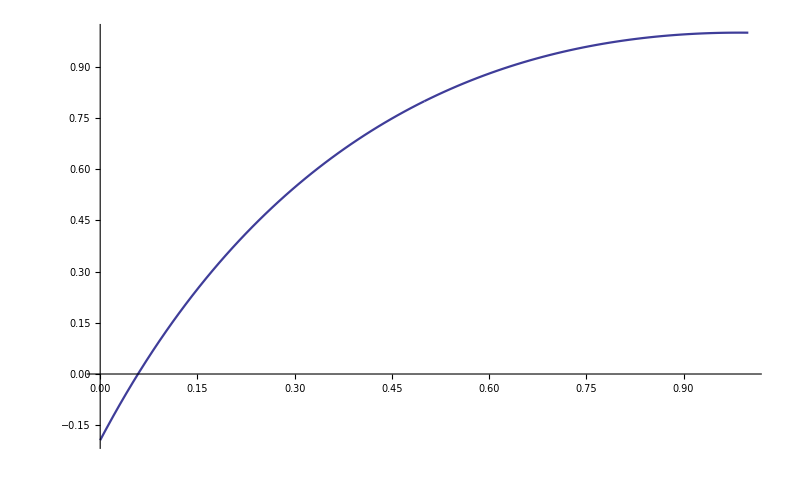

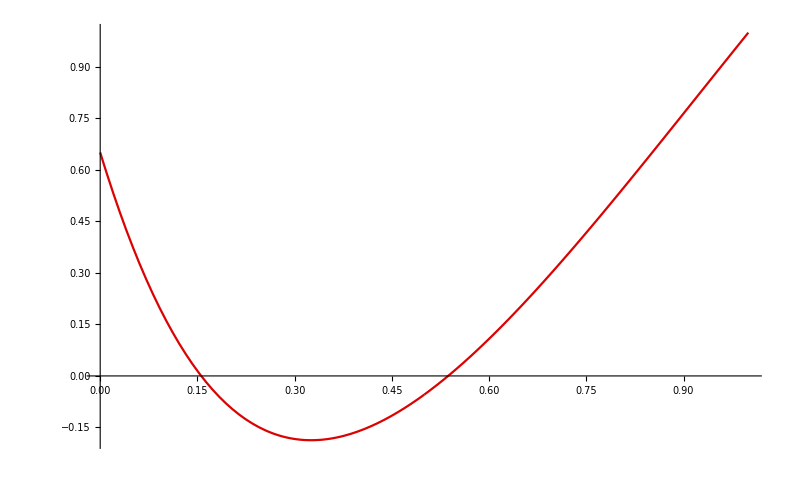

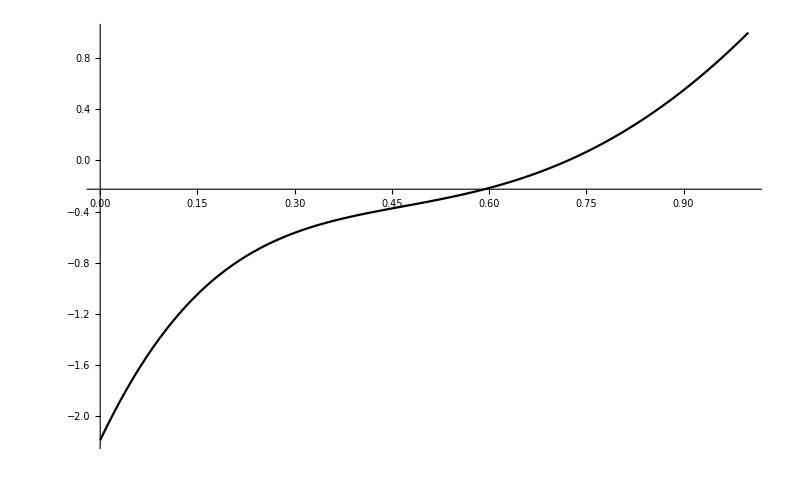

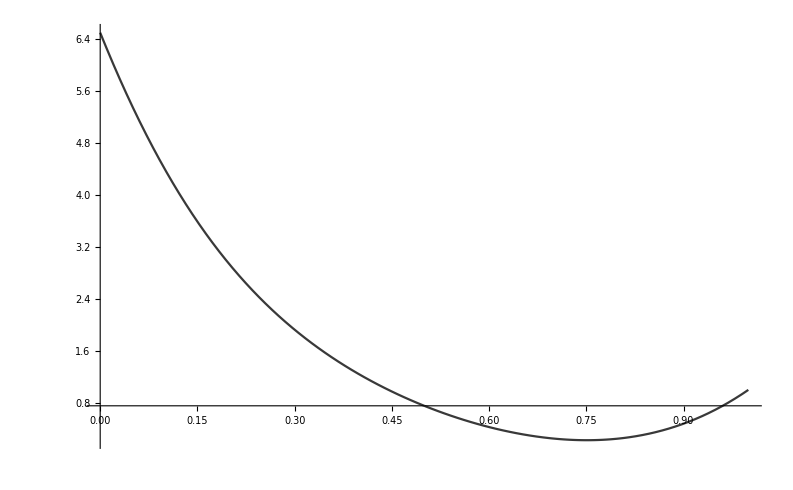

Part::partw: Part 5 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

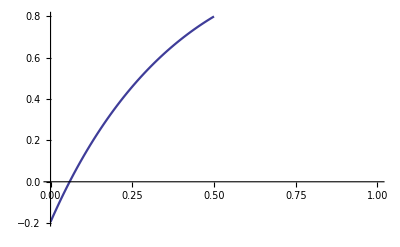
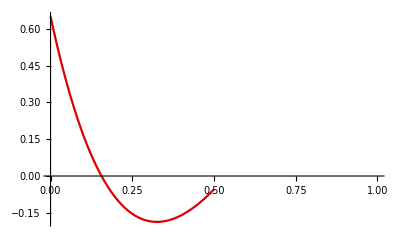
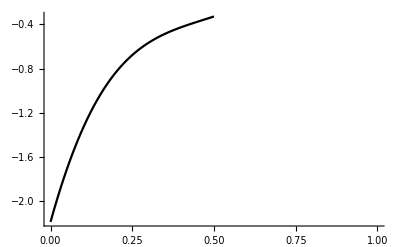
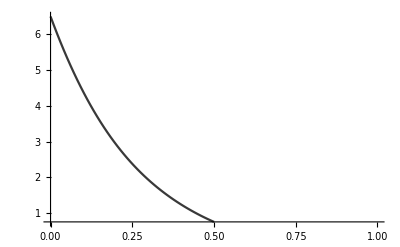
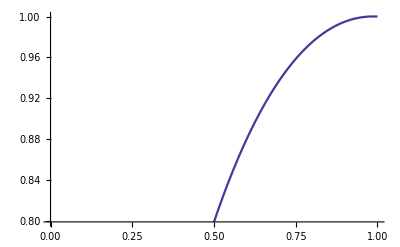
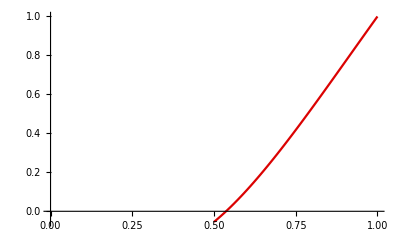
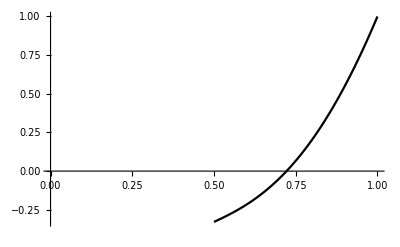
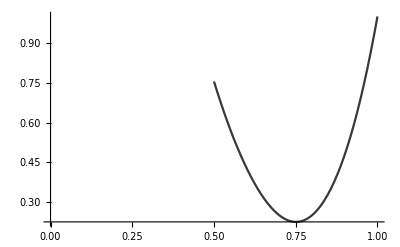
Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦5⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦5⟧]

Part::partw: Part 6 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦6⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦6⟧]

Part::partw: Part 7 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦7⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦7⟧]

Part::partw: Part 8 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦8⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦8⟧]

Part::partw: Part 9 of {,,,} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦9⟧,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}⟦9⟧]

```mathematica
Show[Plot$ϕQNM$Func$dom0[[1]],Plot$ϕQNM$Func$dom1[[1]]]
Show[Plot$ϕQNM$Func$dom0[[2]],Plot$ϕQNM$Func$dom1[[2]]]
Show[Plot$ϕQNM$Func$dom0[[3]],Plot$ϕQNM$Func$dom1[[3]]]
Show[Plot$ϕQNM$Func$dom0[[4]],Plot$ϕQNM$Func$dom1[[4]]]
Show[Plot$ϕQNM$Func$dom0[[5]],Plot$ϕQNM$Func$dom1[[5]]]
Show[Plot$ϕQNM$Func$dom0[[6]],Plot$ϕQNM$Func$dom1[[6]]]
Show[Plot$ϕQNM$Func$dom0[[7]],Plot$ϕQNM$Func$dom1[[7]]]
Show[Plot$ϕQNM$Func$dom0[[8]],Plot$ϕQNM$Func$dom1[[8]]]
Show[Plot$ϕQNM$Func$dom0[[9]],Plot$ϕQNM$Func$dom1[[9]]]
```

## QNM Amplitudes

## QNM Excitation Operators

### Operators

```mathematica
A$dom0[s_]:=- W$dom0*s^2*Id$dom0 + L1$dom0 + s*L2$dom0;
c$dom0[s_, sQNM_]:=L2$dom0- W$dom0*(s+sQNM)*Id$dom0;
B$dom0[s_,V0_,W0_]:=L2$dom0 . V0 - W$dom0*(s*V0 + W0);

A$dom1[s_]:=- W$dom1*s^2*Id$dom1 + L1$dom1 + s*L2$dom1;
c$dom1[s_, sQNM_]:=L2$dom1- W$dom1*(s+sQNM)*Id$dom1;
B$dom1[s_,V0_,W0_]:=L2$dom1 . V0 - W$dom1*(s*V0 + W0);
```

#### Choose QNM

```mathematica
An$dom0=Table[A$dom0[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom0=Table[c$dom0[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom0[[iQNM]],{iQNM,1,n$QNM$max}];

An$dom1=Table[A$dom1[s$QNM[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$dom1=Table[c$dom1[s$QNM[[iQNM]],s$QNM[[iQNM]]].ϕQNM$dom1[[iQNM]],{iQNM,1,n$QNM$max}];

(*An$Conj=Table[A[s$QNM$Conj[[iQNM]]],{iQNM,1,n$QNM$max}];
Cn$Conj=Table[c[s$QNM$Conj[[iQNM]],s$QNM$Conj[[iQNM]]].ϕQNM$Conj$Vec[[iQNM]],{iQNM,1,n$QNM$max}];*)
```

#### Multidomain Matrix

```mathematica
An=Table[ N[ArrayFlatten[{
{   An$dom0[[iQNM]]    ,       Zero$dom0dom1   } , 
{  Zero$dom1dom0,   An$dom1[[iQNM]] } 
}],
Prec],
{iQNM,1,n$QNM$max}
];


Cn=Table[ Join[Cn$dom0[[iQNM]],Cn$dom1[[iQNM]]],{iQNM,1,n$QNM$max}];
```

#### Continuity of Auxiliary function at Boundary Domain

```mathematica
An[[All,1,All]]=0;
An[[All,1,1]]=1;
An[[All,1,-1]]=-1;

Cn[[All,1]]=0;
```

#### Continuity of Auxiliary function’s derivative at Boundary Domain

```mathematica
An[[All,nz$dom0 + nz$dom1,All]]=0;
An[[All,nz$dom0 + nz$dom1, ;;nz$dom0]]=Dσ$dom0[[1, All]];
An[[All,nz$dom0 + nz$dom1, nz$dom0+1;;nz$dom0+nz$dom1 ]]=-Dσ$dom1[[-1, All]];

Cn[[All,-1]]=0;
```

```mathematica
Length@An[[1,1,1]]
```

0

## Calculate QNM Excitation Factor

```mathematica
ϕ$s=LinearSolve[An[[1]],Cn[[1]]];
```

```mathematica
ϕ$s
```

{4.116596526063796490921713407496315435184572691430451183182482090418116841760471837338645131338805530960982900602729821911450779779819055641876634×10^39-2.256498164053185502762617975880271708527395589497076158715018345892963776956183410319711926291143712356475119496778302545171788300494903060510037×10^39 ⅈ,4.116300032778117564454605117202741730772204305878429995748554191763447179986122680709555002916305568019947779447307039107554338650882207298615723×10^39-2.257373898972179219804234526241180642470998600973622410477367513481526370390209947605558956324608024035201806751052091050832798313477895560921491×10^39 ⅈ,4.115410095134842884111555271912979245292734565513730930356538454119687202276597593178326915295019595886900411355547638687819485012207351445227997×10^39-2.259999877533466426867689530905619799969223287199049767745859476778327419930284184824336661801907835869292321030524571521148095729033646701130397×10^39 ⅈ,4.113925330741666817603355488776497674413651294380463776209585349838892570774683928530237137735287051308817731886001700119523768485440167755333737×10^39-2.264372463295202061048472914999695780375993704820509594110531418462828974020112743070558490015953538880126291012417058125170706179234280116580606×10^39 ⅈ,4.111843405397374084818936680042599901879165692752373536197085121226546560479632697158549791114355362619631880150653321855368047226129143864987043×10^39-2.270485735123271117699068276926788681013390876942227569775365476794476825777808549582339742087884512500771747774594510485907471748214865898786073×10^39 ⅈ,4.109160987422363632459120532078542302784395401802685322210594128679679253041305605545078789071115771428900610137536093464934092866559132531153312×10^39-2.278331693528208617997063383537012445135779433211242848391515402211258395755982800684059776323687686378553356033772691575202302579366252682717582×10^39 ⅈ,4.105873683055660121898392532671453094573527061123251682550702757860966072580590169468096932953190119815856764135181871083836449830683261996437886×10^39-2.287900543474742631849471240803857652255412472769575874460730175417320703424161756737969992232821141646639077940130770583646831490654860469301442×10^39 ⅈ,4.101975952323074772175892797126970401478713610260655432056898347741965668278658240451854401694941676914392757902932698170394941207608179404642535×10^39-2.299181047764772096235204051422779950180975675743985144966912478156192216599528721658091359996730744706958365536335944498178493400474221123167304×10^39 ⅈ,4.097461004706138196894204634659884632765725320413829406625930598364720418297952681288984762013421638361272022144943950501168767395418952956293803×10^39-2.312160943635649988268361383240338353448061513359121144941006310420350100475477906392202493869989422518364183488213973045810627967299720880890557×10^39 ⅈ,4.092320673928601640446097610242734546685192611140343545921427295464353163629392898674386483825613968242527106925209573050372256231053111405680001×10^39-2.326827413915901205203260223234122251496147274927509344231928845238455804247837975159715238933626800522949039500807495995603864112459332806194188×10^39 ⅈ,4.086545271231431603216829578556090583215867243413624240571705936163174004117149863269614460304588602634866545258676779222656347668247999558369349×10^39-2.343167602963920237144364928998619540086486501118908197895072520178333916089783675593341345296237109259094904445727165311807956992001591537904358×10^39 ⅈ,4.080123416628901219441323409875367556426602358337194998173922856067472158072175294087875305571520764733543086284939092347044914616658548395838259×10^39-2.361169166699528111648821172122040352892594893488198017838473761058595525591926521260599539983086378433481986745494715927068319230364944222510647×10^39 ⅈ,4.073041847824327228179540251437994716070847590082762624768438647700990712450805157747871028682438092545454554595094856165162994355876372352071381×10^39-2.380820845334544231525412116867029062067316829981430790195084516926815552684097621277436151608421342270998371166912231219508354958900010156069442×10^39 ⅈ,4.065285206707666570161446052063236004231179758488294222770688177364861948982345548214613460802072713374545583231608110501106936049485241674788435×10^39-2.402113046920758327343832958728982412154786372939189784735893007076455638266626744845792458113877648404410566706212371204359014572346934700549127×10^39 ⅈ,4.056835803649664805119842602184983702443216252514791620346684497195818969703223311041536602017321546165391173600853170777797514285079153207433405×10^39-2.425038429558890257364206556097180005882524052929513745378502296479152071264009324760949185733731273928670092191602837451351293705940761911257064×10^39 ⅈ,4.047673360138396809367567320288366292128448350354063818719285337399819938458020048885576264397518669632540878493700168515420884718620416998359862×10^39-2.449592470040648791550728650428220482161394776607170233663663817704443561579893314604229726154225168644911104775352733783862167895419903488750179×10^39 ⅈ,4.037774730663730262197635284370016200957397285438044533639561514015943047806631383478977388465168929990231811621855086935779071732117464037696252×10^39-2.47577400681214033022292034391650463808770524920236140801119350911213670843346191735118412580161377917169780918623054475936880486026098630232471×10^39 ⅈ,4.027113605134640475523680178749688379594785392004013960763868693263778008670838816778382025906558113350746366173990421810884886384333933591353025×10^39-2.503585745429777336844495204833689692791124005993560835378512928892096062488148285757006123706266363901854323149002157283077300681938607292803466×10^39 ⅈ,4.015660193507083994741722219370976278888902957687657470721961431147521275873345851315511327991937724569648243496269392719859949173757017040028824×10^39-2.533034715104632006430157313074868105451919989516238368473147947244824990740271797545068706862184901963592779433265996417716795024182132069842821×10^39 ⅈ,4.003380894703533224219462411995649511032461928095439594917353958450990962260843024252878297318529702757139995115251264193254175772629453382427324×10^39-2.56413266547035842551774727207106521288965486659612016648691012073320620687012925153670469730738999122270836008477710319350345699592374378228086×10^39 ⅈ,3.990237952320908338926880338022290798860107277522252916509106676219543822957096230878979971124335109652079168393985797820708295211061837525512992×10^39-2.596896393334698230150384982807556903559803433968784441959909226649692531441507296336407433722519491498559491548694898060515979959768824592630372×10^39 ⅈ,3.976189100058069088554614283389714196077977929208914557591781942130433220502398912071426587163106086463554031176829241470336785349518969945406949×10^39-2.631347989856953626602110756761385566992365920622765633519592197582620309517583065484268668031044657160975369489957529962260974799152525039304965×10^39 ⅈ,3.961187200258955740107278305982271130693580205685840905051811956438207848736980055501405341727923205854635546049040952639512562215304821465421605×10^39-2.667514999307452762939580170273858986539127864735487234714568448616972581863063359201478581309181764601257173669465735091122813909115050017861754×10^39 ⅈ,3.94517987947965374488740326915308411376290513757448241481353607175531399038795810216696804336324039598001710984622115311326421462601726487175248×10^39-2.705430481287323368830316539685857165164563210617048173839006074424892408023892159618458254225427863094520692491297265648884138922477127971513736×10^39 ⅈ,3.928109165568481598483794949430052582037268580449273311099854360788657264261734033412888155948945585297963323226482063518301973677231849733179249×10^39-2.745132969000226917232874603499645146300417273048718450493699360631908645527539385487933194222017597907735316770122328321407303008320324134062481×10^39 ⅈ,3.909911131422936399692601912777894930389298723729125579801328774045601924878518827991016125940053815972569334874876976864353365592490173070172822×10^39-2.786666316860764599236451177551488749583947617346840747635191180449245390204472427622787376989103256101865839099608539892581643114546433949914675×10^39 ⅈ,3.890515551384126719394359398217917320924027903749875507103829556697711681628983823241876202763819258551039134126258040308364007786895498194775402×10^39-2.8300794313930498104873284006922430516056926744281488455780298023028731980189900546464990677954361848770347269897459775090785439129515777822721×10^39 ⅈ,3.869845577177947321387638889370083616118181397918504871638798839525433230800555422612557074478940307470052595105684281070162632026699109990788791×10^39-2.875425880021557611773985597397715078279176535621611815285356577440817063525858808379127176891215146198417941641803461023841399285605966609835595×10^39 ⅈ,3.847817441442611428869033183001984030835457793254875335937943991786307288130686574401736533261972965056044826651424965460765043387566564494460841×10^39-2.92276337299751384508924512576659682937438660488561695511820739915492299903392200016099124355300947325694268475967981743069461443136870553295817×10^39 ⅈ,3.824340198222606827773222498719556885530968007580516134342516283877317347894985546651030325331344396503171616680863620634161985423178232316645291×10^39-2.972153114359247899714985016208195809184266108280225463159700092842524828805833383912086631735699579274415216629808372194891402307650589475981515×10^39 ⅈ,3.799315511384591888071187797756128786702601877507651274484750273756455559607503593698307003218701607624181221891138292882102477109783397892204269×10^39-3.023659018524177454718712298594381858558186947803223544054457277689447003568665044228330555701351694126456142940993928904061216362387096114848891×10^39 ⅈ,3.772637503740565948289228214078012388727572604569366360286715433319516806079012342322439131405416180276415276372435833865137374409231099994301242×10^39-3.077346789891565452953573969922964372510388899077203445522867404578364087491556962348280511000125437388688989502340753680480069190074867883998451×10^39 ⅈ,3.744192681759343639087584538480694262226299281070976878236588628729854826657887972834402471359177864651723757029115859206794262848176441662695786×10^39-3.133282863744180621791622487080708224230476549620179241615982731352427504323523407709544070198057678439275854033272537227748826731180737099680671×10^39 ⅈ,3.713859953110011029023855060399341565799418288580216219200661614037284235848993147792435467905559729973994899230717926897998824064011025418494421×10^39-3.191533207824584530410674535418612096725480966494687279753807640456076334036238758265707348726060901820005311319389738731306074153218145010110675×10^39 ⅈ,3.681510756898437468963148494666849127231923730198751888097434681860314166362736730763863596616948513677216404936984504115081348108732814559424352×10^39-3.252161985282987065264811901384097102975567633188756466972611938449121354527994621581452396595709531406803162442478123408622837878519673263077155×10^39 ⅈ,3.647009329301415841516167811782116211814340677352394490820061648956199979294128480261232604984863624412063534648059777911430045314447935063485524×10^39-3.315230081305026519374390576173697548381762406185696424670935717783088618470798711971667546736045131134258784015892657880091422331045974621002374×10^39 ⅈ,3.610213130324037486548467663394343275034680541656206756473546758116253171338420971149496521300868721800828017004627866297138065197672022259359084×10^39-3.380793497684501119360250612169810080980279818066844243872654789712459375908934077703371014990568786014872858810335551577541471971735888048370887×10^39 ⅈ,3.570973460532171441888014929869342034867738122509568779315967476322486497552158856317479659721608316622505291182954457988434572225181534820579692×10^39-3.448901621957766764298787977152945338039229773584381285953510781158494967674091151144623185111616509740603575570002181486737482649520310793462092×10^39 ⅈ,3.529136299743245371204542231376318670110870565501058107880769554880439079149127046922805818274773943409580943105938644408676333911928713988854601×10^39-3.519595380503045572133157424304422561804332897119688797870954360037611347967881232115513020125204195571077893285613436329089678525098709546314667×10^39 ⅈ,3.484543402662506715137393027247879951723277358498116580256234160386549238269307773966997899411186648210141615519843262401971330028787232245766505×10^39-3.592905288253582918922534010762843595514088887530210218810846474644012250758307370223552244450573451744061689842666406670627061398133196619444194×10^39 ⅈ,3.43703368915935797369761669745994938764315930116417926254120999518912861977792151761248363891943899886015457129065475417355928577830629547380161×10^39-3.66884941138072167033406328400270184976693945785895432586348218293268386856409381637299553177237102213391731162791294807495928373145105245053078×10^39 ⅈ,3.38644496907856443400436220102979987113399143045615866321767118314778853160415729510275419302571334739355081340681707676118713581813389796572125×10^39-3.747431263444267443768345201125695303783549193475081095374775668177762074205539292125216644483116305946298674934249549712962957163699683840639232×10^39 ⅈ,3.332616042917549562518030300544009045828147855401622492589930332372715229719387115316579064774687413665158826442918870432882483568328008174553394×10^39-3.828637660017909822956626433262290288061291390346776507328194081292538629084497012543528410037158609792074064759117928345046162075940111902602316×10^39 ⅈ,3.275389220066939598633238655154955618390357485089783193052309719004161524568120643903224303330231082879098392595350878470697021754583012607164496×10^39-3.912436561565293242555164173002642269084530890462857746513622344577592639687425453759221769684670701179438618901593430394396914285191224161567351×10^39 ⅈ,3.214613295246641307498406407555705927078883714288853419955459514339703190478314083384942978547672814099603402065773645066935367332269589091899773×10^39-3.998774939200821811871402774427619540524581853780261617959441935561747934531417457082526049842808758209408010424296173697437448590967829863303931×10^39 ⅈ,3.15014702085742931228996182194772560612929695498194095814607954598064145583889908788848182415534564965017148870464396027928630763177893323069627×10^39-4.087576702689122376039917664993949032041300385787495893046945215050981675208833510317956084361757574722210109259856912423845666092025340752181966×10^39 ⅈ,3.081863107734328089705344904926257470302094371303142477850391149128410335238387204677594860490572258114004943871188820402052104149813057941168938×10^39-4.178740734321659633607766458847575475559868576682856729160397884191885161027808687970439018421224578168334109846833060717519152896103279808183132×10^39 ⅈ,3.009652778702820737192474624797827747181069163611866138083441019878791961388002090068694548352501903232443436870907666629219109972530838430350517×10^39-4.272139075794316657588185730821256955758678528013425551311373587622920486917282904247186710215902027248552824880543290908647999092104673068782008×10^39 ⅈ,2.933430887820149615211472210239052574042630267944764532551832826719847979005159772913978725865236521441768237085481842252429264421706076067441178×10^39-4.367615317471937940141006008688542399685219424828971308153505280017705459011368495703121210632637783290127151578154068116618698022402523291011611×10^39 ⅈ,2.853141602607464702294369898681138020009868740195882747104934468990639036654356462646587001626653876232686618138791388554612011136945693048449465×10^39-4.464983239999574071579430313329846366439634351571320423726194453311892020669521311384505893126423914854265749866926511196320844862412004375862704×10^39 ⅈ,2.768764626295068615492492692749286289685772164235490910150204681728704239214609657462010190503517932627144299860942764423267310634626622050107584×10^39-4.564025756632438931822918143442928009037135676278397813594029273081937942174945288815609329044930121507049304224731916173902129555331735492187964×10^39 ⅈ,2.680321911467393102089651893722282435111294591187976498882917823539695610505116807216597647397426433566457057246417442119008400946803379220272338×10^39-4.66449420048004484402426728052598052907860018466270488875875791133124932746963222243884460168398521202916165227297519467033318854631242596498568×10^39 ⅈ,2.58788478491301063172002594790729087685109799570523703824524404177089458176989849285472073659705055168238912645283293483120144990267873856889959×10^39-4.766107993790119291413698150000785131478580607579677139835827907366204560382612861231691150360037948451598813542687772515624585870701565320551509×10^39 ⅈ,2.491581365490314272759448978430688849645373147491443797076053632253190553351566344430918749026516332337181177084909463504787450873682039704329696×10^39-4.868554726356219448862660495253963320104415531811128496796440120998740858345099402282505118020008332055492368644016442792368186258443401116010772×10^39 ⅈ,2.391604112183457311889849054559629240347523888841241628172333301515461333718534159541098577130475252308587227380721726961050109771887893400919415×10^39-4.97149065739408351716411866079784839668881268712189477855993441196360461433237251579408639111705608753179132491686765894822731801943339782932823×10^39 ⅈ,2.28821728842451286636293289054957090907049733172973410771392700191817614950553812829773203635157488388066337653970798462272801250132971166768258×10^39-5.074541640564988746701936711845945617887507869389490210823599638365349145863695352219402123206112681021632941197027310654458559302673358412880069×10^39 ⅈ,2.181764072017752359714888589883824342114396619994370377619395367348070576845083403669644585789235860490859623806643918950341116879369474962079507×10^39-5.177304456627543490939451521289720567846630251601677857279433198149504182553283920249902039277023187773469264542561841284319310176242202785026126×10^39 ⅈ,2.072672979397279716833566852600013240740049148839654831629397257189371303416208039352934823766574245599216499161756967480239187389003033689904511×10^39-5.279348524585293861846436328811281950671972015660280907871382623058612711042912120560836730238782382321335712483043982566660423860577942893031868×10^39 ⅈ,1.961463211597101813024679770170418945727701532359869891219173244899899646669522073492915006251283943978006995961780523705262705590074919368482855×10^39-5.380217952972070626830651964648079936697800101774457028300526202874252526133262603382870467868050203810541515836587393756085440011916147436575197×10^39 ⅈ,1.848748472087543603481553445194271042730179730318352612812702342019319280895126436143677727077009744347680128056600837027595944613617303696405858×10^39-5.479433891366179289775674266006014215322839497209550940265372049502344767565610101741936648459541142392207497597277880729120721039305412449659972×10^39 ⅈ,1.73523876052225759976920090399906693920129132667664022067581180259442912427360225033966415274733676509396338723540769977637391767911098617958129×10^39-5.576497151621478503958449298331070593776127270021457841731160570825213276664779660067360946471499287342357918217353913301455742748746125832009285×10^39 ⅈ,1.621739620677456205459082736298557582488382519149540025344022456783426621056643972652769885785244572069091670561469481892636784785490738573797329×10^39-5.670891091068999131510918109306164120234653390298315597129061852206674053429772277749144329832194620898204558074843023605835730542998702853949564×10^39 ⅈ,1.509148326579868616936222760329789201039442287220695638928253778224129686670207039323048016557395663750037150142164475267298911015441979014467378×10^39-5.762084786476554653930470740048789116794483625753133804359973527721601734329291743378585648150684875549271228636572285049408320101347128514299914×10^39 ⅈ,1.398446539940481424506304534616818773043867414151534610491831579291717550585352360022239058031083079628683880741713891752236758083636321392823626×10^39-5.849536574911582478042240853255298333933944554093174619259882873157764533170900337244110044470152045143592050400092853089104100184411339907469075×10^39 ⅈ,1.290689075192541227858967584072917393149743631439710205855726977917065003438505785063151510037944129270781002794210620256619521673289177568476826×10^39-5.932698088475716015543668908562534987296528957365981334408379497280316514946010292477147651024118047873497275321987370538073972552630979078373037×10^39 ⅈ,1.18698857206514221248043400127865950393552735358891897544964494909043665729836465369550031637546468803712235290041171662326645077941131373524489×10^39-6.011018952202468052256065496048521247338293460350278692281128721269888888102122856069399578322251796835135917301264129112342984555263834970202369×10^39 ⅈ,1.08849609844361646346474635517669051275845989165537935833890516975900478289592899434628818057034222737240287675743282057463164952146673483525354×10^39-6.083952333020720656100047373698393370395586310237199135635294286721252953828325475422341944559537580173404140705956948276898433026934965549019379×10^39 ⅈ,9.96377976646545876405504668589818678514104537430839559490265473830850445267051271389123002625024519530153214746090481849115096957454834994198619×10^38-6.15096150740388773026862824170003455747011320516504764727466706963488174372461175138014376672039500029844947930102555729626517832762148581008867×10^39 ⅈ,9.11789421557517133423084687153767539728766086074164414419285066725701486129420446216895219042497488019320411506670067195218669843535088488426246×10^38-6.211527545753633262533800319248421219629172055998615469856737814604747523890732589363264038829411721639046484016394882702279196222284714009208391×10^39 ⅈ,8.35845868135429620957110082991179081833730692145116593682950922324486644684166948793203737055663484457285775370489546385273457245144869239675891×10^38-6.265158091912037137616987896580942715826420934703356555715552023059726015901051535340685820574048094586265163531698869089246018916084328494287336×10^39 ⅈ,7.69593114492827225625945195853955288889546778050210398323474981197275298186898529175276649940505156508544784405326941513034267939062000669305194×10^38-6.311397058059737630697518877941872770948213587758591427324827377023738446157339843845147111811414238577006966759331107982393339289096023129489967×10^39 ⅈ,7.13977584613494640907461372966968292427292125277271869865495470193445908626776798800258694035995239326928200311929820849753827089670970940803576×10^38-6.349834881787587200349631530248317986525071915005684123704399925073848975743195289331751222079822246023273080908989673949956908788993843886853708×10^39 ⅈ,6.69818101173959395056943559099166041728614966910527834328474488658220394962732015689097076883907457640517936439418195330066834511291264411526603×10^38-6.380118833361801172447435756959477160174639830229222680786460543644726356676405730787427213663179252811777767287298866632616226049759622839087588×10^39 ⅈ,6.37780545596753104734720666395649592582209934357308784872435053659316668269564312369023419754838553515611259222981473039316477293906018619570482×10^38-6.401962747181676146260201145921033395645688919633172309487117754149131172337313319856775521524008072858518701673978964297189313482534565513381567×10^39 ⅈ,6.18356672960494827452774243491089631362042248226347178349625532826403038396702660381187999705563266006810435446795641050323154224292939514097908×10^38-6.415155505517523088154901562935673705798130118154616183871761518570860670109746528981789324186629449547284783415993263956807941995713114761297806×10^39 ⅈ,6.11848156047956721925356374145577959538362183366999747688725920982726883866849369313693191578992528769852293896377944305864523968523570068726342×10^38-6.419567636933819507983157831514487808818968966307598647282725901551643583218715541388429204749689603331872843933840329884636428615766382069445398×10^39 ⅈ,4.270049468782698271315872495891339613796643727589809972334271192671190715526804213356093650354807639629189032667105677096935069414445399771037515×10^39+9.872626666602460639325474937833082098714803511343506187341184843426884968415311985362479835637552756051554119480770228929883773003360827619620963×10^38 ⅈ,4.27152844350887329228241772380043998470126766036887775859453369864606780556844707340355661779322181742178956140783171159306089252876979529512158×10^39+9.812291677777152842915759864311220159361402761645175343435923574124451501887114482822624799665068479649939776084140301272545465215306073812545992×10^38 ⅈ,4.275908017459050539624401972168637855202082736801049790990277044106129381247472391652035764230216839647965629880514233213825019034742384708865517×10^39+9.631908218482486626809428921259882227853981636702582501604418130329899855228510679445575717553808745716898758121505988076879663953777952845497369×10^38 ⅈ,4.283018750093364189982472448062857349566761351163402037343897692491191673329786202751671401774432355064715316318927811821036210662535715959926906×10^39+9.333336320576813748138368425283968840891660634675712347746834171847742874106361457328119933853602225819442373018675441522120566562055826251910508×10^38 ⅈ,4.292586802657746840636845594471280190335854598538826538713457488673556260864160468616113648435025925430155978113433766506751080153708827791333229×10^39+8.91966046594994628349318786184713945862433461790066410291635415859991124294273316964176243147681764718174072649551301034719022764428862194944329×10^38 ⅈ,4.304246304419128842110531458196384797497586372691035800530221967011605217339687493681002471545329430665575728301793886588578176650515236857212622×10^39+8.39516420696501712066101740138929446720597348977591079933984630677651256911441577858095290008191586015385918442834251474027941372933045609940455×10^38 ⅈ,4.317555737218178732891958228079385801153052176992573756351226734092311131846343466667582778019159348787564345233708565996307195315888068199668508×10^39+7.7652909255586990204430577138152923155239017857582189071777775707260993382038959083311957793333376520272301528382935458081096275632215120897615×10^38 ⅈ,4.332017469785803086128234544390414682647272513762156756146175278318637963849934084936430224354277948895938226131915349427517952273922375982559976×10^39+7.03658776093230454863360249735550319286284519974768092782908379443150026660758605526773643778928892622004864258094758157007869190602742637191062×10^38 ⅈ,4.347099408613171343257134029798355977427931214157709334438979292273215284400243319948680960940208685029790388216395421005145513161511662394424306×10^39+6.21662983477368036921396220195157778135880299348836949389571746792236058021312559282932013912515417206684894971060682499271522901802503880918069×10^38 ⅈ,4.362257626607050460945705794744839913364595754789118314604103636700153652145833826554824889821116700453919197458998174249585379431751304452766647×10^39+5.31392253722419731602557100244476406088360680962680143648084409897889405236914617803814078141371862656742709070491112688605037307461305419218401×10^38 ⅈ,4.376958792538024780865063590085396707080029304073980404711525801099102895905236857630832128090064123756788969315241833923890594015347970732538429×10^39+4.33778075837179867911949947184125856098518783813735638985302199667841536876054705791212197823047730741456882409957848197479362297149248993653239×10^38 ⅈ,4.390701257754516114708216192969155364286460711682999297717074682380459488255218021027323241295262137674550881596740068736947727341809126533550716×10^39+3.29818544613895180249283051558617017642248096632901392290617160090141741473236676261934396397346200262885540088727081714703057962407432247654459×10^38 ⅈ,4.403033761285504273749994138507342653798490795435466437238390802326027381516317314570757646405705045663433013654280875480713110840453798387744655×10^39+2.20561957884968869091544488928176169980122524203116216331624824614195951165713422137344403607447744132177959512544813541318681529336015459866101×10^38 ⅈ,4.41357088428846171576452111917093965477678912482747559768318322945388136658936294997186120743841237702799116651131394552037670058894930091630991×10^39+1.07088736698473726998753513524813354894842200172877781280968034495378887339793855209039604166054712135120119469947909198619394213555180901241961×10^38 ⅈ,4.422004608240393120578248821424883899450981088017213468862267409235880507300410075230619202973107738077723123461417060349039639756840467050316147×10^39-9.5077953224840164619273903959539235583888638220487964847100774714678420778396874877208779348869888263547281135220193469217831699299192398584896×10^36 ⅈ,4.428111591780930056858763250211174058936951706147450480791171166778804726425195071700327367177546952538853261537599253163290105484952332444955477×10^39-1.28141117764321818513125834075583838526782770206771903291224752267752241425395399074596990372347210208188330489189713400887352535278538236386783×10^38 ⅈ,4.43175605851852237739135278850321163165405343165491067814778180090816207695415911106847016331685829917150878268656222676128216101189655685812019×10^39-2.47750977988544662108699104907182896501842515350808042411147416715227952450130285300096759545300595382237466636438652190322458313841717978424309×10^38 ⅈ,4.432888460498810495080004864553226592574719515440971341046148649506899174250591555144364526489974181513663057149521445019024510759667581842921793×10^39-3.67321873607196847021860057867479229998554300470601869344883579444730988009337227460777555641705254328344937076325288196743097450886097571246415×10^38 ⅈ,4.431540328044436122929235045257533050453319807746782910401853991235300386629197792511852712853494480451228937161327486193170893041396583989474009×10^39-4.85899854593529024498206853305801716501507608480589953639906564041639552957571654235532741322540666481276650012574566422717355390919085984256584×10^38 ⅈ,4.427815917784708510885026539766837551885488627991375342234225371846937236596077395004656352952468234478137854047433942346621503426714705635204523×10^39-6.02607041055670105362403292887693770940120684026164983541489472583986963751433078698328622831505056006797154075010675724843405365175667155415586×10^38 ⅈ,4.421881413204974306241646616775891947872248537342437897599595008618065045340577102257778828818664245734087413383481011988285179472870093314833605×10^39-7.16653388053211446368070519928070949801280802308389227240984832868042600617515727324482457156866253120253729417943267238844296769239345579711253×10^38 ⅈ,4.413952508458458716977256805128204364800336460687064470810961463796919396101927476133455899181939994582783204977428538780771743919439076797425751×10^39-8.2734539101140767095138458257082501673167173273729443143229605832013032200208098978615460463023193522936409416014230042706388452266888889483509×10^38 ⅈ,4.404281215744894930332430961303389622658601995217159432793458843188938934512437958391750526623720750689946470296789089541960103543386220677745216×10^39-9.34091598495467232648417735905432958420646611867292459489293225349470855681605085129444058440468029802691722452637303721251644193564731274448263×10^38 ⅈ,4.393142684937797260471025272932606577021493430458056931942910122136094838697319895678860498375852591432194603274241274719500198130846081754660195×10^39-1.036404967995181162816577156837573217691717171861391245679832786584606349695587059221307098869745037572054453564274637686105837594336229430600535×10^39 ⅈ,4.38082272230154636107414930639460780101600000875104892176768910532460086922164496098474587050053947720810728199565397372257815023945108761798214×10^39-1.133902251720158119624875869373445914520984194912360271064636281579907600705155463339890281358473011372692213693990486636924775045075952675639289×10^39 ⅈ,4.367606557640821084941170052368837069412669370804221001205493163373150260890015737863233290382977916089127831996592875220291328195165893436039754×10^39-1.226300723326501855701026006952753990032856645344860980325725538523464095292320495636896239165222661624113801319191270749064788338042936894308386×10^39 ⅈ,4.35376925222946385517622590563421243806769293332022399914534763972877612267700027530346938539291465200640569751569473120269538835236623813190014×10^39-1.313412647010252867271670897333068878591276638875616591481189447743553776091767919909669380740749233494786954846406322331961670714030301978847421×10^39 ⅈ,4.339567979166179797069832234321631768491207665760963852552862276483629325229698782578010594130011258943809232050450778823745714482954784892726778×10^39-1.395137945454827323445700358961477420085598035490813824696246780965482723601744261890645843793470630340606657547792468689964946096705200120056128×10^39 ⅈ,4.325236257156402460120688405117315467832996572010972900527276609117324386659853445466051726327669296390141195646287679630612069147390809305656807×10^39-1.471455544101208215870995382143112626296727514762359751528759088537098489460077926011894011323736889515625692802615832902587889845855759289910505×10^39 ⅈ,4.310980088670239097409769578480016052584593882567262252282248613280533917007141475700910758968587928165614805626152573285461855230283164780937262×10^39-1.542413860173999394779705732586527148719943965622682321311146347150015131224149052621026379974042968363362547627557711711411963765448098237085114×10^39 ⅈ,4.296975850726515879151306139188954885615234367104511952832484254730289337970836060509281343295724676241226620533979931518602129443781035822930065×10^39-1.608120871627981362729457013674342413008047575289872622098740752539296408678261238076062985592803632008175746108425902387108943347739125325200095×10^39 ⅈ,4.283369714137623958832017560126146002050060587757869674671221625832455709962066321655383288830607468629401448026707019114051951139534835910887247×10^39-1.668734150276115705975591043929215414910571657319619786781987579503675630626474340867976292584860404761144645208157404234278059779365472869555599×10^39 ⅈ,4.270278324483876062100015521324028196476606287018440180489705433225022406570254617241103159155887321832308453247020202248137590358622436379020965×10^39-1.72445118143992451165920832607115901537614295028896277670594261394279040917243068874470053669088478090722530887412111242914144463650548906178216×10^39 ⅈ,4.257790462320471296018738846383282954961666497995297054686304052176810183996369934814929504691442812059992100330182656450756251879474289073359839×10^39-1.775500225566360077272301436704785527853334444304363524672353581211434368391118191061985222387326754561421280131287222977232912799792656035446389×10^39 ⅈ,4.245969406390817785148057449496226188249676734191989167367162993287882782892030842467392565328287021475477347518739869205184846730207288371808777×10^39-1.822131910453144310359469927130482933858193324563966499934202716412362275289270771580974910271597274005225548734725692674167857693135448068956885×10^39 ⅈ,4.234855746335947527034494323696766649142787814584140846507334089651474134174559862094312733476559781428726644674794354453754227057620945459992116×10^39-1.864611679929734889289523302793310840681476287176525645712446253126404122416118702688872161263848338468548505258471987988250331266572354133217896×10^39 ⅈ,4.224470424897669822841694573638484170320020463546730570068805896151269955522679276344352071903048189683574627440341374278345707775427403518030075×10^39-1.903213168779117687210598078386444299518519780004815582746988419095403540325033377835841578334293004576106598290502381706182063993199607363229929×10^39 ⅈ,4.214817828770898773576760271312621167774622842736776234417153316004932485502828491583703642000261981176094062712869143616356615088970084111552343×10^39-1.93821252598446117715574590592283722220178105174544178663839607548362197087752802645576735828790001405942890639323587377115094542772635208736675×10^39 ⅈ,4.205888787799746707816420315155030786497196259109375735121291225347491904783037123815771924886009464793597841809901702021440396849724014125003041×10^39-1.969883669737139367739521307085929785531180106333014270122471102123147377838729426820958718756130700299080887935077994671862582006764572950183407×10^39 ⅈ,4.197663380902803056943620312142469750942044741212189461769051319646367364500687283022305342759131270773861956703794213532662475448757180235226568×10^39-1.998494428003514588630644857720153183976654426928289558691936582007951597749847047638160617668501963341864554325555579187723255663241624654545611×10^39 ⅈ,4.190113481770646078752497059981825253641994608685318285019201945927684726944325620922558508659073370073750253183924060469771520462794654707655994×10^39-2.024303497235739050876632115671267721384154507230580504936152884517497372113235760620947999109648827962544377305794080013915182673059604075150226×10^39 ⅈ,4.183205006757459121702047795573562880036481835826490379161159545002208599208081029156814959482922597974920243328510369485097094178952165972643496×10^39-2.047558138095433288332239393143262536997661502125768372241938038061219247586019080067306084859350609723807785443911714750817711353498264143607516×10^39 ⅈ,4.176899851012536421196794818717541343772723276774222338393204585290231150077178302447098654906182070423969282342178707077866615403911455137012338×10^39-2.06849251971639661579770262313028189669675001401707390865749095726659585854364416218434421709862262294055700502644971570758492086798271976843279×10^39 ⅈ,4.171157516866052231405651728750667711570684744314922126283057540096823890666387372378504887582427038145732284338454491268399180301667189903986418×10^39-2.087326621877173936967311466043189154341864565559770416788492049125211737846607778263026439863726242340929560559344819089000219315888338737626924×10^39 ⅈ,4.16593645128388054765469231964009988691724836129328581281660949838273852760658627059803853309582849233937867083312779645574940248022694443323204×10^39-2.104265606329309682827213786035110166532302621552172506628917846898404524513730703003259624544075522248345451692974369465776536024860647327733585×10^39 ⅈ,4.161195117549493324866785520659318856698104211272495052245220898011356368873517678534564551224738761107330332860847644799490914574562976101083164×10^39-2.119499573368161110637641237863211927010436967196275536712736431749998357675125954659503591569091207249997225166781074535585123774565508667502541×10^39 ⅈ,4.156892831021781383841889896331887890487856938745355746357859113842998219715538146246126980820388372594462153910129035178329672078574939274781404×10^39-2.133203626606450226314290718276705741870468172903760973054691700050206670304466845346037766587126179111804677170734515828094369347018101896168145×10^39 ⅈ,4.15299039065992505361616523446724003591323729455247591015081886688803275908218553775060802167075289195105311831929122410264498962106394932797552×10^39-2.145538177030415306987529670818544117997961872469062047185401665351121729701493370850708453492082053230032863365325484093673999790788098113167778×10^39 ⅈ,4.149450537741227024287604874272041844955093644641906906065978186461716401683129330481703205511020410279114732251333436230157042969402808398087075×10^39-2.156649426148517616218057651484190228094806052213197414108386733217895532808710063333586908188810033194758565596632465367979364125154975478598408×10^39 ⅈ,4.146238271468390742477782664086212495256219090725720893122697969230241468161011310571331945221389221864969236078139333310529616422684902030444056×10^39-2.166669976888578142078505732571154244415278320880912997792541816544901913898217627534546147661360279005698923146289391595347146150266029303662442×10^39 ⅈ,4.143321048500384100130944273914337074686146367465056531188261107077116449583453310861133931744175393403773459701499788221258781845924081751197722×10^39-2.175719529492572454852108219091154342090677382491699181183782437013091047302468575239006521475924249733104397072243220568963035788442529965685655×10^39 ⅈ,4.14066889026530456039672931118122906868918795742487642839526006355422036843997390863482656953891825629750719499153421772477011000884687071204011×10^39-2.183905627738311427495601667415418445222632450213653368791570938523429684186158040703664156577897472964150656417390792491463937633259890391910898×10^39 ⅈ,4.138254418541622264906082618139900613440752866761982124835760126293047307924165795715060893528296226474028186846596411807335056271765199051128894×10^39-2.19132442821111666385057213141399836874923173412847779057340670576173529617783980739277390886706762296472211351121370947224020017476979404555888×10^39 ⅈ,4.136052836454546401501747562336309658697412303391214220381467519884376229907454867712681491413485679301758470569489089312390932073368904711010853×10^39-2.198061471952794827551916271917636672474874921013697386334878957364200505028081070593004802522210518275525303085951047559253961368077671604259272×10^39 ⅈ,4.134041868883290134316234248732410441737364158477072594782890889052192959558666487671395174284651029080012044151799470758371255004339176153201224×10^39-2.204192443578436061752441795078383526726911393201531644614496394841749672699768928526807808566742556212245027118250744290753243918602152341763106×10^39 ⅈ,4.132201673412010110847206378822889790561162017100112646006364780102059889737971289963112676332130531892173715002876195841726594204481956549615538×10^39-2.209783907860455407270251731486054032994970616082229925376923684394608407548725756113709665686532760496784227950995120025094913599940518495995372×10^39 ⅈ,4.130514730438470991855069773112631613307651423735108725493811097229961324420141674147111056639263101982061663242241838738255392027076443463040785×10^39-2.214894017846971584654804145667574560874114061180519950379726420795480973952428381087462037907385592212186852467648823333024448977388789658556556×10^39 ⅈ,4.128965718905051083094297090997479979638093479683235090479030125780610594353659890654718761383090186000533863757684483954607585240646043571580319×10^39-2.219573191839047219932858574720611802434193005099173318540145345575284241524363659780857659681551372496429547266266327185922166859341400561980037×10^39 ⅈ,4.127541382339612315808555761441294998036364990951007084632672872184046038678661106924655498441366765224694560514310562431598024610207907551100315×10^39-2.223864759041405283788993576109926340394923057362569525148911715941312259358265671007135979468938174582724291075059071789131080367676896420455989×10^39 ⅈ,4.126230388477107437232387673170069577640837391416481355917897152782232018050806296908705379008396189935766383363680355602690803722996308270387605×10^39-2.227805575475211308191833634831387444002829342659864667980391393406764983420952044365486366068278376761920716429478665703424674583897955590532657×10^39 ⅈ,4.125023184654731855566961076340871119132406910335958215039047489230480547364173407738804653634171479584691889457605207795163703493303319909957721×10^39-2.231426612857143014543009266296764375995224635550522329469533160558476378183507137056545330339592785892146011715280036684093173616296814890657429×10^39 ⅈ,4.123911850405458849552068369857713815242011899783305148352002773485907212394043723298685360252431169752675832863135629068215340854733487992528097×10^39-2.234753523670145447839917122437490421476116110490047342794999213346127716966589013619610280863777789910837778626204508827463178647328231355682323×10^39 ⅈ,4.122889948183865786504928945498621910868247643559254052635698430484445381280307847846903688790415437156477091541935368201797387293498863728535021×10^39-2.237807185648340479802589173709745360280665467312467716989371100248356606398886707762240909569797697332295422369371875190338364251738395448403488×10^39 ⅈ,4.121952372907819715493034863527998085189707098358470493784535698544537115679207817711268382583433702937435427922454030152499498435713529977935702×10^39-2.240604228448936917878679780633398880686554243049202395920798806810256508157906838423465752858326146338218007007124091361613907951415026945558162×10^39 ⅈ,4.121095200950680027131143512080756561439155891852993760866840975725806033928717774538630440391876051667603232563782796496934031061967450814547468×10^39-2.243157544472508015469776381833053781081861003194911793370723341710318772353043151866490466483509416372661480695580503351662897741626106406012115×10^39 ⅈ,4.120315539329783946663819165628305988402409236380270686610944153011200352362513648043227104335836705391123241354246640728325288715544018365042216×10^39-2.245476784711643638897606152779780070129407881366865486291543523887991430968971094434697616024393277188572493288687710834359392229329213821440591×10^39 ⅈ,4.119611376064978511629166982822844078081335333272053059551135468707472067125190603563385475961713959272512389883353912642391517603255453891610096×10^39-2.24756883925463486423367711812641559929877235562314827885575860395840437691449151009827089219663893002258879361347245850462530753999927335473187×10^39 ⅈ,4.118981432981772559384868568086305026626751356094816522448704229716681741011964443949003280429887969643558498477551340542686637415811974779120636×10^39-2.24943830074698560617847142542859995253523868651829270647132290987769295887062782253906970198845001174708484148155829339410933366770375392430487×10^39 ⅈ,4.118425022563397534266796042723474455819872216054071495879874215578625738322674037844918482785470240516365260577572711866938673986497806154133096×10^39-2.251087907820801397075251021924537683558220893906165561303179215010303222311767183186287980809736207212069287392042723317985501679411439837426813×10^39 ⅈ,4.117941910772445282384185964812960808330780475068591589897398473768575963969845297092947696690581500593292931775781170530955939765169639748328967×10^39-2.252518964337894696807956338617548544331721558319421238294744873701137457727354762351350727086902667224497107498903615885322332682561153928333955×10^39 ⅈ,4.117532188027027198305214007710560196998321583722291543005415067320008462042849549364688066974493068332900877186736304567472471644953263927781539×10^39-2.253731729344959955985975437916258195853284814774050107213444970578132244360133918927774288497818457407837874144615450705294550449841491198964733×10^39 ⅈ,4.117196150695268053987878819030115955474843510282254182885794728362048352682282642916430594889999319012841389063083111986781495534916687903775534×10^39-2.25472577198216991879353737323414881859913391652676799316096396262759235215917725573504359670816037306769225758062586286638098608920050995306141×10^39 ⅈ,4.116934195539543326832829811604246401811504088794154140516708635110932756095232303159594364814890491312059169722044947786892010249483844726204696×10^39-2.255500285274463680356517489396497552254428376966974622039070335503804396081497526905891898534327788320073557184615498066700467009588675755498167×10^39 ⅈ,4.116746729481492028839124356163849844303134247662747728610051345100883961191186132587610258701703925596279525865130265720871798591120410693014655×10^39-2.256054352798710005336556558647938639129330130953675143393617349196172389983685823546737456189265676977079748766522922243754549239700150620144147×10^39 ⅈ,4.116634096864205142355005290324054840088420716509842761650534391504125898612932495848888091928572288072219023814072728357363331187447693737415142×10^39-2.256387162664859636604845002266873492867159969948885985481384272185412728910024083655206995752059646466315532823081333533202244880071529277937063×10^39 ⅈ,4.116596526063796490921713407496315435184572691430451183182482090418116841760471837338645131338805530960982900602729821911450779779819055641876634×10^39-2.256498164053185502762617975880271708527395589497076158715018345892963776956183410319711926291143712356475119496778302545171788300494903060510037×10^39 ⅈ}